# Dark Matter Imprints on the Ringdown of Kalb–Ramond Black Holes

```mathematica
Needs["PacletManager`"]
```

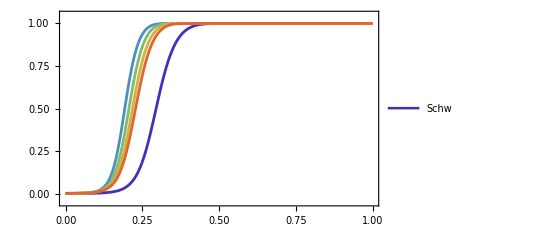

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFk01.pdf

```mathematica
Clear["Global`*"]

<<MaTeX`;

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=2;
lval=1;

kval=0.1;

lambdaValues={0.1,0.2,0.3,0.4};

(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;

(*Scalar perturbation potential:V(r)=f(r)[l(l+1)/r^2+f'(r)/r]*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r )];

(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];

(* ======================================================*)
(*Position of the maximum of the potential*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum found at boundary for lambda = ",lamN];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];

(* ======================================================*)
(*Third-order WKB QNM frequency*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
(*Derivatives with respect to the tortoise coordinate:d/dr_* =f(r) d/dr*)ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
(*Third-order WKB equation:b=I (Omega^2-V0)/S-part1-part2 Therefore:Omega^2=V0-I S (b+part1+part2)*)omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];

(* ======================================================*)
(*QNM data for n=0 and n=1*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lam,0,lval,kval,Mval];
w1=QNMFrequency[lam,1,lval,kval,Mval];
{lam,w0,w1}],{lam,lambdaValues}];

QNMData//TableForm;

lambdaClean=QNMData[[All,1]];
w0List=QNMData[[All,2]];
w1List=QNMData[[All,3]];

(* ======================================================*)
(*Schwarzschild reference values*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;
wsch1=0.26221187146850566-0.3074323472728198 I;

(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyEikonalFormula[w0_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])];

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2)*(1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0])*(1+((Re[w0]-Re[w1]) Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1]) Re[w0]^2)/(12 Im[w0]^3))];

GBFactor[x_]:=1/(1+Exp[2 I Pi x]);

Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];

(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];

GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];

TransmissionList=Transmission/@GBList;

(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBFk01=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["\\lambda/M = "<>ToString[NumberForm[lambdaClean[[i]],{3,1}]],Magnification->1.3],{i,Length[lambdaClean]}]],{0.8,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFk01.pdf",GBFk01,"PDF"]

(*GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1.},{-0.05,1.05}},Frame->True,FrameStyle->Thickness[0.004],FrameLabel->{"ω","Γ(ω)"},PlotLegends->Placed[LineLegend[{Black,Blue,Red,Green,Orange},{"","=0.1","λ=0.2","λ=0.3","λ=0.4"}],{{0.8,0.2},{0.3,0.2}}],PlotStyle->{Black,Blue,Red,Green,Orange},LabelStyle->Directive[Black,14],Axes->False,BaseStyle->{{FontFamily->"Times"}},AspectRatio->9/16];

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.},PlotRange->{{0,1.},{-0.05,1.05}},PlotLegends->Placed[Join[{""},Table[Row[{"λ = ",NumberForm[lambdaClean[[i]],{2,1}]}],{i,Length[lambdaClean]}]],{0.8,0.4}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["ω",18],Style["Γ(ω)",18]},LabelStyle->Directive[Black,14],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]];
*)
```

```mathematica
7
```

7

## mass=0.2 k=0.1 λ = 0,..0.4

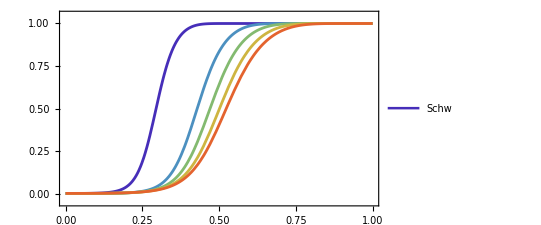

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFk01m02.pdf

```mathematica
Clear["Global`*"]

<<MaTeX`;

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

kval=0.1;

lambdaValues={0.1,0.2,0.3,0.4};

(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;

(*Scalar perturbation potential:V(r)=f(r)[l(l+1)/r^2+f'(r)/r]*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r + 0.2^2)];

(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];

(* ======================================================*)
(*Position of the maximum of the potential*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum found at boundary for lambda = ",lamN];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];

(* ======================================================*)
(*Third-order WKB QNM frequency*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
(*Derivatives with respect to the tortoise coordinate:d/dr_* =f(r) d/dr*)ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
(*Third-order WKB equation:b=I (Omega^2-V0)/S-part1-part2 Therefore:Omega^2=V0-I S (b+part1+part2)*)omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];

(* ======================================================*)
(*QNM data for n=0 and n=1*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lam,0,lval,kval,Mval];
w1=QNMFrequency[lam,1,lval,kval,Mval];
{lam,w0,w1}],{lam,lambdaValues}];

QNMData//TableForm;

lambdaClean=QNMData[[All,1]];
w0List=QNMData[[All,2]];
w1List=QNMData[[All,3]];

(* ======================================================*)
(*Schwarzschild reference values*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;
wsch1=0.26221187146850566-0.3074323472728198 I;

(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyEikonalFormula[w0_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])];

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2)*(1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0])*(1+((Re[w0]-Re[w1]) Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1]) Re[w0]^2)/(12 Im[w0]^3))];

GBFactor[x_]:=1/(1+Exp[2 I Pi x]);

Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];

(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];

GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];

TransmissionList=Transmission/@GBList;

(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBFk01m02=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["\\lambda = "<>ToString[NumberForm[lambdaClean[[i]],{3,1}]],Magnification->1.3],{i,Length[lambdaClean]}]],{0.83,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFk01m02.pdf",GBFk01m02,"PDF"]

(*GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1.},{-0.05,1.05}},Frame->True,FrameStyle->Thickness[0.004],FrameLabel->{"ω","Γ(ω)"},PlotLegends->Placed[LineLegend[{Black,Blue,Red,Green,Orange},{"","=0.1","λ=0.2","λ=0.3","λ=0.4"}],{{0.8,0.2},{0.3,0.2}}],PlotStyle->{Black,Blue,Red,Green,Orange},LabelStyle->Directive[Black,14],Axes->False,BaseStyle->{{FontFamily->"Times"}},AspectRatio->9/16];

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.},PlotRange->{{0,1.},{-0.05,1.05}},PlotLegends->Placed[Join[{""},Table[Row[{"λ = ",NumberForm[lambdaClean[[i]],{2,1}]}],{i,Length[lambdaClean]}]],{0.8,0.4}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{Style["ω",18],Style["Γ(ω)",18]},LabelStyle->Directive[Black,14],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]];
*)
```

BH threshold = 0.210819

Schwarzschild threshold = 0.2

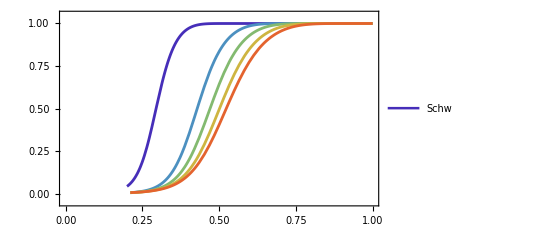

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFk01m02.pdf

```mathematica
(* ======================================================*)(*Physical propagation thresholds*)(* ======================================================*)mval=0.2;

omegaThresholdBH=mval/Sqrt[1-kval];
omegaThresholdSchw=mval;

Print["BH threshold = ",N[omegaThresholdBH]];
Print["Schwarzschild threshold = ",N[omegaThresholdSchw]];


(* ======================================================*)
(*Individual physical curves*)
(* ======================================================*)

schwPlot=Plot[Transmission[GBSch][ω],{ω,omegaThresholdSchw,1},PlotRange->All,PlotStyle->Directive[ColorData["Rainbow"][0.1],Thickness[0.005]]];

lambdaPlots=Table[Plot[TransmissionList[[i]][ω],{ω,omegaThresholdBH,1},PlotRange->All,PlotStyle->Directive[ColorData["Rainbow"][0.1+0.2 i],Thickness[0.005]]],{i,Length[lambdaClean]}];


(* ======================================================*)
(*Final plot*)
(* ======================================================*)

GBFk01m02=Legended[Show[Prepend[lambdaPlots,schwPlot],PlotRange->{{0,1},{-0.05,1.05}},Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{FontFamily->"Times"},AspectRatio->9/16],Placed[LineLegend[Join[{Directive[ColorData["Rainbow"][0.1],Thickness[0.005]]},Table[Directive[ColorData["Rainbow"][0.1+0.2 i],Thickness[0.005]],{i,Length[lambdaClean]}]],Join[{"Schw"},Table[MaTeX["\\lambda/M="<>ToString[NumberForm[lambdaClean[[i]],{3,1}]],Magnification->1.3],{i,Length[lambdaClean]}]]],{0.82,0.42}]]


Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFk01m02.pdf",GBFk01m02,"PDF"]
```

```mathematica
Table[{om,Transmission[GBSch][om]},{om,{0.2,0.21,0.22,0.23,0.24,0.25,0.26,0.28,0.30}}]//TableForm
```

0.2 | 0.0425261
0.21 | 0.0579867
0.22 | 0.0788247
0.23 | 0.10648
0.24 | 0.142431
0.25 | 0.187937
0.26 | 0.243662
0.28 | 0.383067
0.3 | 0.542534

```mathematica
Table[{om,TransmissionList[[1]][om]},{om,{0.21082,0.22,0.23,0.24,0.25,0.30}}]//TableForm
```

0.21082 | 0.00585934
0.22 | 0.00712964
0.23 | 0.00886982
0.24 | 0.0110813
0.25 | 0.013893
0.3 | 0.0441872

## GBFactor for k{0.1, 0.2, 0.3, 0.4} values

Get::noopen: Cannot open MaTeX`.

$Failed

k

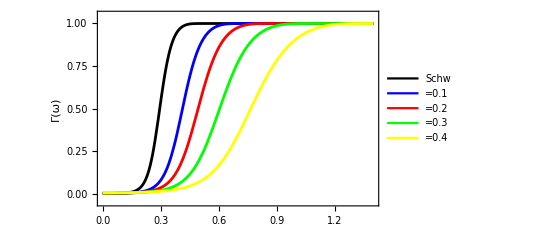

```mathematica
Clear["Global`*"]
<<MaTeX`

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

(*fixed lambda,varying k*)
lambdaVal=0.1;

kValues={0.1,0.2,0.3,0.4};


(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;


(*Scalar perturbation potential*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r)];


(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];


(* ======================================================*)
(*Position of potential maximum*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum at boundary"];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];


(* ======================================================*)
(*Third-order WKB QNM*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];


(* ======================================================*)
(*QNM data varying k*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lambdaVal,0,lval,k,Mval];
w1=QNMFrequency[lambdaVal,1,lval,k,Mval];
{k,w0,w1}],{k,kValues}];


QNMData//TableForm;


kClean=QNMData[[All,1]];

w0List=QNMData[[All,2]];
w1List=QNMData[[All,3]];


(* ======================================================*)
(*Schwarzschild reference*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;

wsch1=0.26221187146850566-0.3074323472728198 I;


(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2) (1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0]) (1+((Re[w0]-Re[w1])Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1])Re[w0]^2)/(12 Im[w0]^3))];


GBFactor[x_]:=1/(1+Exp[2 I Pi x]);


Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];


(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];


GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];


TransmissionList=Transmission/@GBList;


(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.4},PlotRange->{{0,1.4},{-0.05,1.05}},Frame->True,FrameStyle->Thickness[0.005],FrameLabel->{"","Γ(ω)"},PlotLegends->Placed[LineLegend[{Black,Blue,Red,Green,Yellow},{"Schw","=0.1","=0.2","=0.3","=0.4"}],{{0.8,0.2},{0.3,0.2}}],PlotStyle->{Black,Blue,Red,Green,Yellow},LabelStyle->Directive[Black,14],Axes->False,BaseStyle->{{FontFamily->"Times"}},AspectRatio->9/16]

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[Join[{MaTeX["\\text{Schwarzschild}"]},Table[MaTeX[" = "NumberForm[kClean[[i]]],Magnification->14/10],{i,Length[kClean]}]],Center],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->20/12]&)/@{"\\omega","\\Gamma(\\omega)"},LabelStyle->Directive[Black,14],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]];
```

## GBFactor for k{0.1, 0.2, 0.3, 0.4} values new Code rainbow stayle

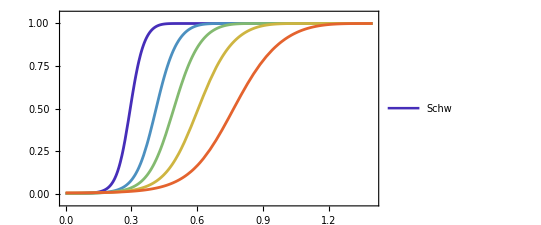

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01.pdf

```mathematica
Clear["Global`*"]
<<MaTeX`

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

(*fixed lambda,varying k*)
lambdaVal=0.1;

kValues={0.1,0.2,0.3,0.4};


(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;


(*Scalar perturbation potential*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r)];


(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];


(* ======================================================*)
(*Position of potential maximum*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum at boundary"];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];


(* ======================================================*)
(*Third-order WKB QNM*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];


(* ======================================================*)
(*QNM data varying k*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lambdaVal,0,lval,k,Mval];
w1=QNMFrequency[lambdaVal,1,lval,k,Mval];
{k,w0,w1}],{k,kValues}];


QNMData//TableForm;


kClean=QNMData[[All,1]];

w0List=QNMData[[All,2]];
w1List=QNMData[[All,3]];


(* ======================================================*)
(*Schwarzschild reference*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;

wsch1=0.26221187146850566-0.3074323472728198 I;


(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2) (1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0]) (1+((Re[w0]-Re[w1])Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1])Re[w0]^2)/(12 Im[w0]^3))];


GBFactor[x_]:=1/(1+Exp[2 I Pi x]);


Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];


(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];


GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];


TransmissionList=Transmission/@GBList;


(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBFlambd01=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.4},PlotRange->{{0,1.4},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["k = "<>ToString[NumberForm[kClean[[i]],{3,1}]],Magnification->1.3],{i,Length[kClean]}]],{0.85,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01.pdf",GBFlambd01,"PDF"]

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[LineLegend[Join[{Black},ColorData["Rainbow"]/@{0.2,0.4,0.6,0.8}],Join[{TraditionalForm[""]},Table[TraditionalForm[Row[{Style["k",Italic]," = ",kClean[[i]]}]],{i,Length[kClean]}]]],{0.75,0.35}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{TraditionalForm[Style["ω"]],TraditionalForm[Style["Γ(ω)",Italic]]},LabelStyle->Directive[Black,12],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]];
```

## GBFactor for k{0.1, 0.2, 0.3, 0.4} values new Code rainbow stayle

```mathematica
Clear["Global`*"]
<<MaTeX`

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

(*fixed lambda,varying k*)
lambdaVal=0.1;

kValues={0.1,0.2,0.3,0.4};


(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;


(*Scalar perturbation potential*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r)];


(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];


(* ======================================================*)
(*Position of potential maximum*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum at boundary"];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];


(* ======================================================*)
(*Third-order WKB QNM*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];


(* ======================================================*)
(*QNM data varying k*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lambdaVal,0,lval,k,Mval];
w1=QNMFrequency[lambdaVal,1,lval,k,Mval];
{k,w0,w1}],{k,kValues}];


QNMData//TableForm;


kClean=QNMData[[All,1]];

w0List=QNMData[[All,2]];
w1List=QNMData[[All,3]];


(* ======================================================*)
(*Schwarzschild reference*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;

wsch1=0.26221187146850566-0.3074323472728198 I;


(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2) (1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0]) (1+((Re[w0]-Re[w1])Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1])Re[w0]^2)/(12 Im[w0]^3))];


GBFactor[x_]:=1/(1+Exp[2 I Pi x]);


Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];


(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];


GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];


TransmissionList=Transmission/@GBList;


(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBFlambd01=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.4},PlotRange->{{0,1.4},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["k = "<>ToString[NumberForm[kClean[[i]],{3,1}]],Magnification->1.3],{i,Length[kClean]}]],{0.85,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\omega","\\Gamma(\\omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/GBFlambd01.pdf",GBFlambd01,"PDF"]

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[LineLegend[Join[{Black},ColorData["Rainbow"]/@{0.2,0.4,0.6,0.8}],Join[{TraditionalForm[""]},Table[TraditionalForm[Row[{Style["k",Italic]," = ",kClean[[i]]}]],{i,Length[kClean]}]]],{0.75,0.35}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{TraditionalForm[Style["ω"]],TraditionalForm[Style["Γ(ω)",Italic]]},LabelStyle->Directive[Black,12],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]];
```

-Graphics-

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/GBFlambd01.pdf

## GBFactor for k{0.1, 0.2, 0.3, 0.4} values new Code rainbow stayle

```mathematica
Clear["Global`*"]
<<MaTeX`

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

(*fixed lambda,varying k*)
lambdaVal=0.1;

kValues={0.1,0.2,0.3,0.4};


(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;


(*Scalar perturbation potential*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r)];


(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];


(* ======================================================*)
(*Position of potential maximum*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum at boundary"];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];


(* ======================================================*)
(*Third-order WKB QNM*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];


(* ======================================================*)
(*QNM data varying k*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lambdaVal,0,lval,k,Mval];
w1=QNMFrequency[lambdaVal,1,lval,k,Mval];
{k,w0,w1}],{k,kValues}];


QNMData//TableForm;


kClean=QNMData[[All,1]];

w0List=QNMData[[All,2]];
w1List=QNMData[[All,3]];


(* ======================================================*)
(*Schwarzschild reference*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;

wsch1=0.26221187146850566-0.3074323472728198 I;


(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2) (1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0]) (1+((Re[w0]-Re[w1])Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1])Re[w0]^2)/(12 Im[w0]^3))];


GBFactor[x_]:=1/(1+Exp[2 I Pi x]);


Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];


(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];


GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];


TransmissionList=Transmission/@GBList;


(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBFlambd01=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.4},PlotRange->{{0,1.4},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["k = "<>ToString[NumberForm[kClean[[i]],{3,1}]],Magnification->1.3],{i,Length[kClean]}]],{0.85,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\omega","\\Gamma(\\omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/GBFlambd01.pdf",GBFlambd01,"PDF"]

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[LineLegend[Join[{Black},ColorData["Rainbow"]/@{0.2,0.4,0.6,0.8}],Join[{TraditionalForm[""]},Table[TraditionalForm[Row[{Style["k",Italic]," = ",kClean[[i]]}]],{i,Length[kClean]}]]],{0.75,0.35}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{TraditionalForm[Style["ω"]],TraditionalForm[Style["Γ(ω)",Italic]]},LabelStyle->Directive[Black,12],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]];
```

-Graphics-

/Users/bakhodir/Theoretical Astrophysics/4thProjectQNM/GBFlambd01.pdf

## m=0.2 λ=0.1 k=0,..,0.4

0.1 | 0.421132-0.138661 ⅈ | 0.359967-0.459135 ⅈ
0.2 | 0.499085-0.177579 ⅈ | 0.425757-0.58425 ⅈ
0.3 | 0.606939-0.234139 ⅈ | 0.515779-0.766551 ⅈ
0.4 | 0.763475-0.321015 ⅈ | 0.645001-1.04727 ⅈ

{0.1,0.2,0.3,0.4}

{0.421132-0.138661 ⅈ,0.499085-0.177579 ⅈ,0.606939-0.234139 ⅈ,0.763475-0.321015 ⅈ}

{0.359967-0.459135 ⅈ,0.425757-0.58425 ⅈ,0.515779-0.766551 ⅈ,0.645001-1.04727 ⅈ}

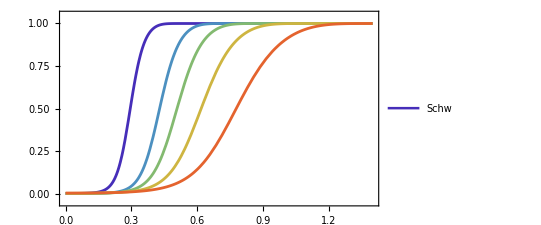

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01m02.pdf

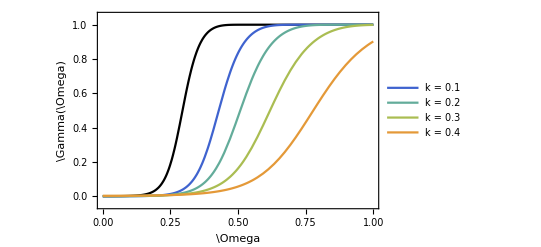

```mathematica
Clear["Global`*"]
<<MaTeX`

(* ======================================================*)
(*Parameters*)
(* ======================================================*)

Mval=1;
lval=1;

(*fixed lambda,varying k*)
lambdaVal=0.1;

kValues={0.1,0.2,0.3,0.4};


(* ======================================================*)
(*Metric function*)
(* ======================================================*)

fBH[r_,lam_,k_,M_]:=1/(1-k)-(2 M)/r+lam/r Log[r/lam];

fpBH[r_,lam_,k_,M_]:=2 M/r^2+lam (1-Log[r/lam])/r^2;


(*Scalar perturbation potential*)

VBH[r_,l_,lam_,k_,M_]:=Simplify[fBH[r,lam,k,M]*(l (l+1)/r^2+fpBH[r,lam,k,M]/r + 0.2^2)];


(* ======================================================*)
(*Event horizon*)
(* ======================================================*)

rhBH[lam_,k_,M_]:=N[lam (1-k) ProductLog[Exp[2 M/lam]/(1-k)]];


(* ======================================================*)
(*Position of potential maximum*)
(* ======================================================*)

rPeakBH[lam_,l_Integer,k_,M_]:=Module[{lamN,kN,MN,rh,rmin,rmax,ngrid,grid,vals,imax,rleft,rmid,rright,dVexpr,root},lamN=N[lam];
kN=N[k];
MN=N[M];
rh=rhBH[lamN,kN,MN];
rmin=rh (1+10^-8);
rmax=100 MN;
ngrid=800;
grid=Subdivide[rmin,rmax,ngrid];
vals=VBH[#,l,lamN,kN,MN]&/@grid;
imax=First[Ordering[vals,-1]];
If[imax==1||imax==Length[grid],Print["Warning: maximum at boundary"];
Return[grid[[imax]]]];
rleft=grid[[imax-1]];
rmid=grid[[imax]];
rright=grid[[imax+1]];
dVexpr=D[VBH[r,l,lamN,kN,MN],r];
root=r/. FindRoot[dVexpr==0,{r,rmid,rleft,rright},MaxIterations->200];
N[root]];


(* ======================================================*)
(*Third-order WKB QNM*)
(* ======================================================*)

QNMFrequency[lam_,n_Integer,l_Integer,k_,M_]:=Module[{lamN,kN,MN,b,r0,fexpr,Vexpr,ders,V0,V1,V2,V3,V4,V5,V6,S,part1,part2,omega2,omegaPlus,omegaMinus},lamN=N[lam];
kN=N[k];
MN=N[M];
b=N[n+1/2];
r0=rPeakBH[lamN,l,kN,MN];
fexpr=fBH[r,lamN,kN,MN];
Vexpr=VBH[r,l,lamN,kN,MN];
ders=NestList[Simplify[fexpr D[#,r]]&,Vexpr,6];
{V0,V1,V2,V3,V4,V5,V6}=N[ders/. r->r0];
S=Sqrt[-2 V2];
part1=I*((1/8)*(V4/V2)*(b^2+1/4)-(1/288)*(7+60 b^2)*(V3/V2)^2)/S;
part2=(b/(2*(-V2)))*((5/6912)*(V3/V2)^4*(77+188 b^2)-(1/384)*(V4*V3^2/V2^3)*(51+100 b^2)+(1/2304)*(V4/V2)^2*(67+68 b^2)+(1/288)*(V5*V3/V2^2)*(19+28 b^2)-(1/288)*(V6/V2)*(5+4 b^2));
omega2=V0-I*S*(b+part1+part2);
omegaPlus=Sqrt[omega2];
omegaMinus=-Sqrt[omega2];
If[Re[omegaPlus]>0&&Im[omegaPlus]<0,N[omegaPlus],N[omegaMinus]]];


(* ======================================================*)
(*QNM data varying k*)
(* ======================================================*)

QNMData=Table[Module[{w0,w1},w0=QNMFrequency[lambdaVal,0,lval,k,Mval];
w1=QNMFrequency[lambdaVal,1,lval,k,Mval];
{k,w0,w1}],{k,kValues}];


QNMData//TableForm


kClean=QNMData[[All,1]]

w0List=QNMData[[All,2]]
w1List=QNMData[[All,3]]


(* ======================================================*)
(*Schwarzschild reference*)
(* ======================================================*)

wsch0=0.29111411637959683-0.09800136312939295 I;

wsch1=0.26221187146850566-0.3074323472728198 I;


(* ======================================================*)
(*Greybody formulas*)
(* ======================================================*)

GreyBodyBeyondEikonalFormula[w0_,w1_]:=Function[ω,-I*(ω^2-Re[w0]^2)/(4 Re[w0] Im[w0])*(1+(Re[w0]-Re[w1])^2/(32 Im[w0]^2)-(3 Im[w0]-Im[w1])/(24 Im[w0]))+I*Re[w0-w1]/(16 Im[w0])+I*(ω^2-Re[w0]^2)^2/(16 Im[w0] Re[w0]^2) (1/Re[w0]+Re[w0-w1]/(4 Im[w0]^2))-I*(ω^2-Re[w0]^2)^3/(32 Re[w0]^5 Im[w0]) (1+((Re[w0]-Re[w1])Re[w0])/(4 Im[w0]^2)+(Re[w0-w1]^2 Re[w0]^2)/(16 Im[w0]^4)-((3 Im[w0]-Im[w1])Re[w0]^2)/(12 Im[w0]^3))];


GBFactor[x_]:=1/(1+Exp[2 I Pi x]);


Transmission[gbfun_]:=Function[ω,Chop[Re[GBFactor[gbfun[ω]]]]];


(* ======================================================*)
(*Greybody functions*)
(* ======================================================*)

GBSch=GreyBodyBeyondEikonalFormula[wsch0,wsch1];


GBList=MapThread[GreyBodyBeyondEikonalFormula,{w0List,w1List}];


TransmissionList=Transmission/@GBList;


(* ======================================================*)
(*Plot*)
(* ======================================================*)

GBFlambd01m02=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1.4},PlotRange->{{0,1.4},{-0.05,1.05}},PlotLegends->Placed[Join[{"Schw"},Table[MaTeX["k = "<>ToString[NumberForm[kClean[[i]],{3,1}]],Magnification->1.3],{i,Length[kClean]}]],{0.85,0.45}],Frame->True,FrameStyle->Thickness[0.005],FrameLabel->(MaTeX[#,Magnification->1.4]&)/@{"\\Omega","\\Gamma(\\Omega)"},LabelStyle->Directive[Black,16],Axes->False,BaseStyle->{{FontFamily->"Times"}},PlotStyle->Table[Directive[ColorData["Rainbow"][i],Thickness[0.005]],{i,0.1,0.9,0.2}],AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/GBFlambd01m02.pdf",GBFlambd01m02,"PDF"]

GBF1=Plot[Evaluate[Join[{Transmission[GBSch][ω]},Table[TransmissionList[[i]][ω],{i,Length[TransmissionList]}]]],{ω,0,1},PlotRange->{{0,1},{-0.05,1.05}},PlotLegends->Placed[LineLegend[Join[{Black},ColorData["Rainbow"]/@{0.2,0.4,0.6,0.8}],Join[{TraditionalForm[""]},Table[TraditionalForm[Row[{Style["k",Italic]," = ",kClean[[i]]}]],{i,Length[kClean]}]]],{0.75,0.35}],Frame->True,FrameStyle->Directive[Black,Thickness[0.005]],FrameLabel->{TraditionalForm[Style["\Omega"]],TraditionalForm[Style["\\Gamma(\\Omega)",Italic]]},LabelStyle->Directive[Black,12],Axes->False,BaseStyle->{FontFamily->"Times"},PlotStyle->Join[{Directive[Black,Thickness[0.004]]},Table[Directive[ColorData["Rainbow"][i],Thickness[0.004]],{i,0.2,0.8,0.2}]]]
```

```mathematica
(* ======================================================*)(*Direct numerical scattering*)(* ======================================================*)ClearAll[DirectScatter];

DirectScatter[omega_?NumericQ,lam_?NumericQ,k_?NumericQ,l_Integer,M_?NumericQ,rMax_:400,eps_:10^-6]:=Module[{rh,r0,omegaTh,chi,xMax,sol,xf,rf,psiF,qF,p,p2,dVdr,dpdr,dpdx,yIn,yOut,qIn,qOut,coeff,AIn,AOut,gammaFlux,gammaReflection,reflection,fluxError},(*m=0.2 is already built into VBH*)omegaTh=0.2/Sqrt[1-k];
If[omega<=omegaTh,Return[<|"Physical"->False,"Threshold"->omegaTh|>]];
chi=Sqrt[omega^2-0.2^2/(1-k)];
rh=rhBH[lam,k,M];
r0=rh+eps;
xMax=2 (1-k) (rMax-r0)+100;
sol=NDSolveValue[{rr'[x]==fBH[rr[x],lam,k,M],psi'[x]==q[x],q'[x]==-(omega^2-VBH[rr[x],l,lam,k,M]) psi[x],rr[0]==r0,psi[0]==1+0 I,q[0]==-I omega,WhenEvent[rr[x]>=rMax,"StopIntegration"]},{rr,psi,q},{x,0,xMax},MaxSteps->Infinity];
xf=sol[[1]]["Domain"][[1,2]];
rf=sol[[1]][xf];
psiF=sol[[2]][xf];
qF=sol[[3]][xf];
(*local asymptotic momentum*)p2=omega^2-VBH[rf,l,lam,k,M];
If[Re[p2]<=0,Return[<|"Physical"->False,"Reason"->"Matching point not yet propagating","rFinal"->rf|>]];
p=Sqrt[p2];
(*derivative of potential*)dVdr=(D[VBH[z,l,lam,k,M],z]/. z->rf);
dpdr=-dVdr/(2 p);
dpdx=fBH[rf,lam,k,M] dpdr;
(*flux-normalized WKB basis*)yIn=1/Sqrt[p];
yOut=1/Sqrt[p];
qIn=(-I p-dpdx/(2 p)) yIn;
qOut=(I p-dpdx/(2 p)) yOut;
coeff=LinearSolve[{{yIn,yOut},{qIn,qOut}},{psiF,qF}];
AIn=coeff[[1]];
AOut=coeff[[2]];
reflection=Abs[AOut]^2/Abs[AIn]^2;
(*because horizon amplitude was normalized to 1*)gammaFlux=omega/Abs[AIn]^2;
gammaReflection=1-reflection;
fluxError=Abs[gammaFlux-gammaReflection];
<|"Physical"->True,"Omega"->omega,"Threshold"->omegaTh,"Chi"->chi,"rHorizon"->rh,"rFinal"->rf,"AIn"->AIn,"AOut"->AOut,"Reflection"->reflection,"GammaFlux"->gammaFlux,"GammaReflection"->gammaReflection,"FluxError"->fluxError|>]
```

```mathematica
test=DirectScatter[0.5,0.1,0.1,1,1,400,10^-6]
```

<|Physical→True,Omega→0.5,Threshold→0.210819,Chi→0.453382,rHorizon→1.55314,rFinal→400.+0. ⅈ,AIn→-0.753113+0.22616 ⅈ,AOut→-0.275528-0.205934 ⅈ,Reflection→0.191362,GammaFlux→0.808633,GammaReflection→0.808638,FluxError→5.54332×10^-6|>

```mathematica
{test["Threshold"],test["Chi"],test["GammaFlux"],test["GammaReflection"],test["FluxError"]}
```

{0.210819,0.453382,0.808633,0.808638,5.54332×10^-6}

```mathematica
rMaxTest=Table[Module[{res},res=DirectScatter[0.5,0.1,0.1,1,1,rM,10^-6];
{rM,res["GammaFlux"],res["GammaReflection"],res["FluxError"]}],{rM,{100,200,400,800,1200}}];

rMaxTest//TableForm
```

100 | 0.808637 | 0.808638 | 1.33702×10^-6
200 | 0.808635 | 0.808638 | 2.77762×10^-6
400 | 0.808633 | 0.808638 | 5.54332×10^-6
800 | 0.808627 | 0.808638 | 0.0000110419
1200 | 0.808622 | 0.808638 | 0.0000164948

```mathematica
epsTest=Table[Module[{res},res=DirectScatter[0.5,0.1,0.1,1,1,400,ep];
{ep,res["GammaFlux"],res["GammaReflection"],res["FluxError"]}],{ep,{10^-4,10^-5,10^-6,10^-7}}];

epsTest//TableForm
```

1/10000 | 0.808673 | 0.808678 | 5.56161×10^-6
1/100000 | 0.808629 | 0.808634 | 5.31195×10^-6
1/1000000 | 0.808633 | 0.808638 | 5.54332×10^-6
1/10000000 | 0.808632 | 0.808638 | 5.61353×10^-6

```mathematica
w0Bench=QNMFrequency[0.1,0,1,0.1,1];

w1Bench=QNMFrequency[0.1,1,1,0.1,1];

gbBench=GreyBodyBeyondEikonalFormula[w0Bench,w1Bench];

gammaQNM05=Transmission[gbBench][0.5];

{test["GammaFlux"],gammaQNM05,Abs[test["GammaFlux"]-gammaQNM05]}
```

{0.808633,0.834817,0.0261841}

```mathematica
omegaTh=0.2/Sqrt[1-0.1];

omegaGrid=N@Subdivide[omegaTh+0.01,1.0,39];
```

```mathematica
directData=Table[Module[{res},res=DirectScatter[om,0.1,0.1,1,1,400,10^-6];
{om,res["GammaReflection"]}],{om,omegaGrid}];
```

```mathematica
qnmData=Table[{om,Transmission[gbBench][om]},{om,omegaGrid}];
```

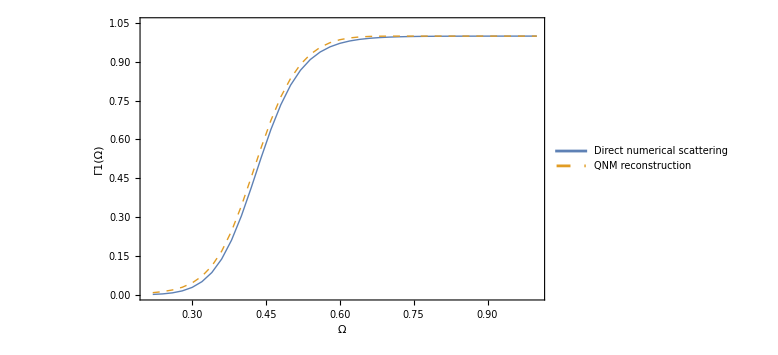

```mathematica
comparisonPlot=ListLinePlot[{directData,qnmData},Frame->True,FrameLabel->{"Ω","Γ1(Ω)"},PlotLegends->{"Direct numerical scattering","QNM reconstruction"},PlotRange->{{omegaTh,1.0},{0,1.05}},PlotStyle->{Directive[Thick],Directive[Thick,Dashed]},ImageSize->Large];

comparisonPlot
```

```mathematica
comparisonTable=MapThread[Function[{d,q},{d[[1]],d[[2]],q[[2]],Abs[d[[2]]-q[[2]]],100*Abs[d[[2]]-q[[2]]]/Max[d[[2]],10^-8]}],{directData,qnmData}];

comparisonTable//TableForm
```

0.220819 | 0.000525633 | 0.00725698 | 0.00673134 | 1280.62
0.240798 | 0.00246365 | 0.0112816 | 0.00881791 | 357.921
0.260777 | 0.00654139 | 0.0177823 | 0.0112409 | 171.842
0.280756 | 0.014205 | 0.0282523 | 0.0140473 | 98.8893
0.300735 | 0.0276441 | 0.0449452 | 0.017301 | 62.5848
0.320714 | 0.0499596 | 0.0710466 | 0.021087 | 42.2081
0.340693 | 0.0851364 | 0.110599 | 0.0254627 | 29.9082
0.360672 | 0.137517 | 0.16783 | 0.0303134 | 22.0435
0.380651 | 0.210436 | 0.245558 | 0.0351223 | 16.6902
0.40063 | 0.304066 | 0.342921 | 0.0388551 | 12.7785
0.420609 | 0.413502 | 0.453802 | 0.0402995 | 9.7459
0.440588 | 0.528955 | 0.567819 | 0.0388639 | 7.34729
0.460567 | 0.638862 | 0.673982 | 0.03512 | 5.49728
0.480546 | 0.734103 | 0.764538 | 0.0304351 | 4.14589
0.500525 | 0.810393 | 0.836468 | 0.0260748 | 3.21755
0.520504 | 0.867902 | 0.890538 | 0.0226359 | 2.60811
0.540483 | 0.909397 | 0.929471 | 0.0200743 | 2.20743
0.560462 | 0.938459 | 0.956484 | 0.0180242 | 1.92062
0.580441 | 0.958428 | 0.974524 | 0.0160958 | 1.6794
0.60042 | 0.971989 | 0.986031 | 0.0140419 | 1.44466
0.620399 | 0.98114 | 0.992946 | 0.0118063 | 1.20333
0.640378 | 0.987295 | 0.996786 | 0.00949153 | 0.961368
0.660357 | 0.99143 | 0.998711 | 0.00728032 | 0.734325
0.680336 | 0.99421 | 0.999557 | 0.005347 | 0.537814
0.700315 | 0.996081 | 0.999874 | 0.00379297 | 0.38079
0.720294 | 0.997342 | 0.999971 | 0.00262922 | 0.263622
0.740273 | 0.998194 | 0.999995 | 0.00180112 | 0.180438
0.760252 | 0.99877 | 0.999999 | 0.00122905 | 0.123057
0.780231 | 0.999161 | 1. | 0.000838736 | 0.083944
0.80021 | 0.999427 | 1. | 0.000573169 | 0.0573497
0.820189 | 0.999608 | 1. | 0.000392329 | 0.0392483
0.840168 | 0.999731 | 1. | 0.000268978 | 0.0269051
0.860147 | 0.999815 | 1. | 0.000184694 | 0.0184729
0.880126 | 0.999873 | 1. | 0.000127008 | 0.0127024
0.900105 | 0.999913 | 1. | 0.0000874613 | 0.0087469
0.920084 | 0.99994 | 1. | 0.0000603074 | 0.0060311
0.940063 | 0.999958 | 1. | 0.0000416345 | 0.00416363
0.960042 | 0.999971 | 1. | 0.0000287758 | 0.00287766
0.980021 | 0.99998 | 1. | 0.0000199095 | 0.00199099
1. | 0.999986 | 1. | 0.0000137892 | 0.00137893

```mathematica
deltaGammaData=MapThread[{#1[[1]],#1[[2]]-#2[[2]]}&,{directData,qnmData}];
```

```mathematica
deltaGammaPlot=ListLinePlot[deltaGammaData,Frame->True,FrameLabel->{"Ω","ΔΓ1"},PlotRange->All,PlotStyle->Directive[Thick],ImageSize->Large];

deltaGammaPlot
```

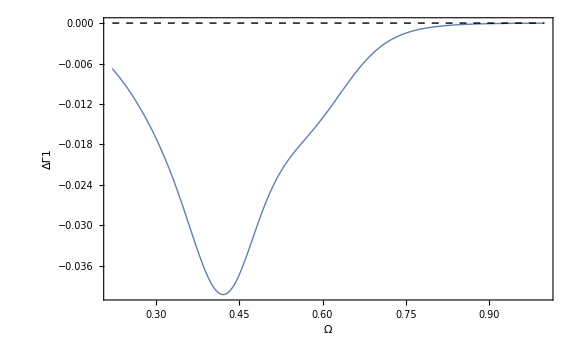

```mathematica
deltaGammaPlot=ListLinePlot[deltaGammaData,InterpolationOrder->10,Frame->True,FrameLabel->{"Ω","ΔΓ1"},PlotRange->All,PlotStyle->Directive[Thick],Epilog->{Dashed,Line[{{Min[deltaGammaData[[All,1]]],0},{Max[deltaGammaData[[All,1]]],0}}]},ImageSize->Large];

deltaGammaPlot
```

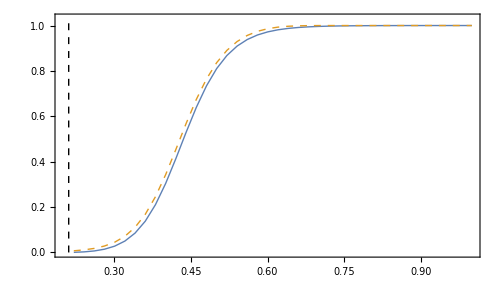

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/panelA.pdf

```mathematica
Needs["MaTeX`"];

(* ================================================*)
(*Panel (a):Direct scattering vs QNM reconstruction*)
(* ================================================*)

panelA=ListLinePlot[{directData,qnmData},Frame->True,Axes->False,FrameLabel->{MaTeX["\\Omega",Magnification->1.2],MaTeX["\\Gamma(\\Omega)",Magnification->1.2]},PlotStyle->{Directive[Thick],Directive[Thick,Dashed]},PlotLegends->Placed[{MaTeX["\\mathrm{Direct\\ numerical\\ scattering}"],MaTeX["\\mathrm{QNM\\ reconstruction}"]},{0.72,0.30}],PlotRange->{{0.2,1.0},{0,1.03}},FrameStyle->Directive[Black,14],FrameTicksStyle->Directive[Black,12],Epilog->{Directive[Black,Dashed,Thin],Line[{{omegaTh,0},{omegaTh,1.03}}]},PlotLabel->MaTeX["\\mathrm{(a)}",Magnification->1.2],ImageSize->500,AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/panelA.pdf",panelA,"PDF"]
```

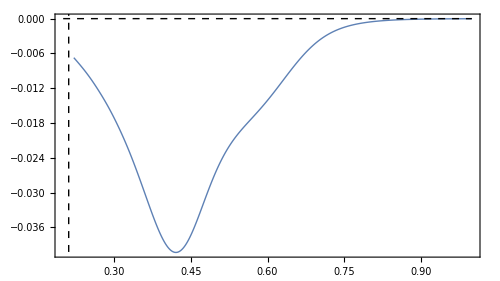

/Users/bakhodir/Theoretical_Physics/4thProjectQNM/panelB.pdf

```mathematica
(* ================================================*)(*Panel (b):Difference*)(* ================================================*)panelB=ListLinePlot[deltaGammaData,InterpolationOrder->10,Frame->True,Axes->False,FrameLabel->{MaTeX["\\Omega",Magnification->1.2],MaTeX["\\Delta\\Gamma",Magnification->1.2]},PlotStyle->Directive[Thick],PlotRange->{{0.2,1.0},All},FrameStyle->Directive[Black,14],FrameTicksStyle->Directive[Black,12],Epilog->{Directive[Black,Dashed,Thin],(*Delta Gamma=0*)Line[{{0.2,0},{1.0,0}}],(*propagation threshold*)Line[{{omegaTh,-0.045},{omegaTh,0.002}}]},PlotLabel->MaTeX["\\mathrm{(b)}",Magnification->1.2],ImageSize->500,AspectRatio->9/16]
Export["/Users/bakhodir/Theoretical_Physics/4thProjectQNM/panelB.pdf",panelB,"PDF"]
```

```mathematica
qnmData={{0.0,0.673839-0.145905 I},{0.1,0.676420-0.144950 I},{0.2,0.684184-0.142071 I},{0.3,0.697191-0.137219 I},{0.4,0.715546-0.130303 I},{0.5,0.739404-0.121177 I}};
```

```mathematica
qnmInfinity={#[[1]],Sqrt[1-#[[1]]] #[[2]]}&/@qnmData
```

{{0.,0.673839-0.145905 ⅈ},{0.1,0.641708-0.137512 ⅈ},{0.2,0.611953-0.127072 ⅈ},{0.3,0.583312-0.114806 ⅈ},{0.4,0.55426-0.100932 ⅈ},{0.5,0.522838-0.0856851 ⅈ}}

```mathematica
reData={#[[1]],Re[#[[2]]]}&/@qnmInfinity;

imData={#[[1]],-Im[#[[2]]]}&/@qnmInfinity;
```

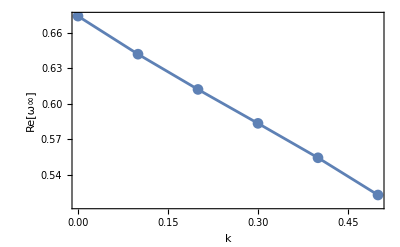

```mathematica
ListLinePlot[reData,Frame->True,FrameLabel->{"k","Re[ω∞]"},PlotMarkers->Automatic]
```

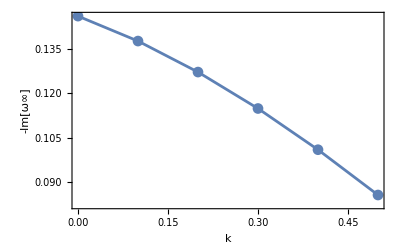

```mathematica
ListLinePlot[imData,Frame->True,FrameLabel->{"k","-Im[ω∞]"},PlotMarkers->Automatic]
```

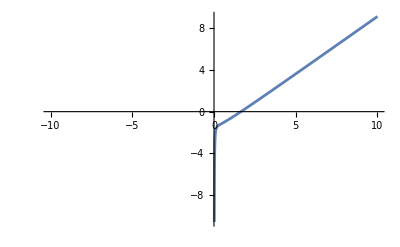

```mathematica
Plot[r/(1-0.1) - 2 + 0.1/r Log[r/0.1],{r,-10,10}]
```